```mathematica
(*raw = Import["~/Downloads/optimizerHistory_200um_0.30Best_noRF.json"];
(*raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"];*)*)

RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]
```

499

491

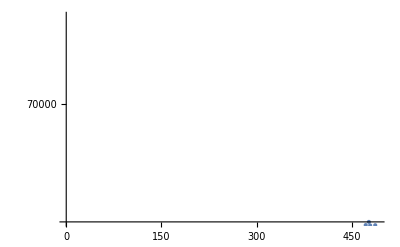

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{1*^4,All},
Joined->False
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|Q1EkG→161.291,Q2EkG→-153.064,Q3EkG→108.372,Q4EkG→133.463,Q5EkG→-19.8374,Q6EkG→-146.573,S1ELkG→871.208,S2ELkG→-1587.49,S3ELkG→-1023.94,S3ERkG→-1118.75,S2ERkG→-1535.07,S1ERkG→1021.17,Q5FFkG→-69.4867,Q4FFkG→-84.2069,Q3FFkG→92.6515,Q2FFkG→125.326,Q1FFkG→-245.565,Q0FFkG→126.843,PDrive_mean_x→4.114×10^-7,PDrive_mean_y→7.308×10^-7,PDrive_sigma_x→0.000295212,PDrive_sigma_y→0.0000531845,PDrive_mean_xp→-0.0000258943,PDrive_mean_yp→2.09×10^-7,PDrive_sigmaSI90_x→0.000205452,PDrive_sigmaSI90_y→0.0000562784,PDrive_emitSI90_x→0.00014967,PDrive_emitSI90_y→9.9521×10^-6,PDrive_zLen→0.0000313446,PDrive_zCentroid→991.332,PWitness_mean_x→-2.3849×10^-6,PWitness_mean_y→-1.779×10^-7,PWitness_sigma_x→0.0000847677,PWitness_sigma_y→0.0000268563,PWitness_mean_xp→-0.00025782,PWitness_mean_yp→2.1159×10^-6,PWitness_sigmaSI90_x→0.0000807199,PWitness_sigmaSI90_y→0.0000257432,PWitness_emitSI90_x→0.0000198744,PWitness_emitSI90_y→4.0179×10^-6,PWitness_zLen→0.0000170867,PWitness_zCentroid→991.332,bunchSpacing→0.000131966,transverseCentroidOffset→2.9403×10^-6,lostChargeFraction→0.,maximizeMe→58407.9|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

Q1EkG : 161.2914282193
Q2EkG : -153.0642557653
Q3EkG : 108.3716236625
Q4EkG : 133.4625285755
Q5EkG : -19.8373791417
Q6EkG : -146.5726431263
S1ELkG : 871.2079323617
S2ELkG : -1587.486278061
S3ELkG : -1023.9384440782
S3ERkG : -1118.7526838298
S2ERkG : -1535.0718980413
S1ERkG : 1021.1681109736
Q5FFkG : -69.4867358227
Q4FFkG : -84.2068735236
Q3FFkG : 92.6515266532
Q2FFkG : 125.3263727914
Q1FFkG : -245.5650519081
Q0FFkG : 126.8432393307
PDrive_mean_x : 4.114e-7
PDrive_mean_y : 7.308e-7
PDrive_sigma_x : 0.0002952116
PDrive_sigma_y : 0.0000531845
PDrive_mean_xp : -0.0000258943
PDrive_mean_yp : 2.09e-7
PDrive_sigmaSI90_x : 0.0002054516
PDrive_sigmaSI90_y : 0.0000562784
PDrive_emitSI90_x : 0.0001496704
PDrive_emitSI90_y : 9.9521e-6
PDrive_zLen : 0.0000313446
PDrive_zCentroid : 991.3317154631
PWitness_mean_x : -2.3849e-6
PWitness_mean_y : -1.779e-7
PWitness_sigma_x : 0.0000847677
PWitness_sigma_y : 0.0000268563
PWitness_mean_xp : -0.00025782
PWitness_mean_yp : 2.1159e-6
PWitness_sigmaSI90_x : 0.0000807199
PWitness_sigmaSI90_y : 0.0000257432
PWitness_emitSI90_x : 0.0000198744
PWitness_emitSI90_y : 4.0179e-6
PWitness_zLen : 0.0000170867
PWitness_zCentroid : 991.3318474287
bunchSpacing : 0.0001319656
transverseCentroidOffset : 2.9403e-6
lostChargeFraction : 0.
maximizeMe : 58407.9159766259

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

2.94024×10^-6

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"L1PhaseSet","L2PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG"}
]
```

{Q0FFkG,Q1EkG,Q1FFkG,Q2EkG,Q2FFkG,Q3EkG,Q3FFkG,Q4EkG,Q4FFkG,Q5EkG,Q5FFkG,Q6EkG,S1ELkG,S1ERkG,S2ELkG,S2ERkG,S3ELkG,S3ERkG}

```mathematica
fitVar = "PDrive_zLen"
```

PDrive_zLen

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVars,
Symbol[#]&/@freeVars
]
```

FittedModel[…]

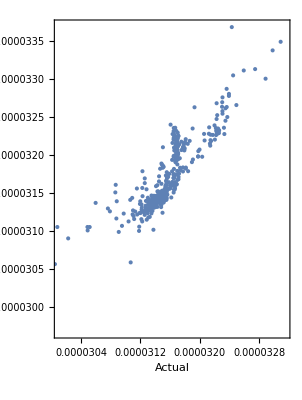

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

```mathematica
Minimize[
lm["BestFit"],
Symbol[#]&/@freeVars
]
```

NMinimize::ubnd: The problem is unbounded.

{-∞,{Q0FFkG→Indeterminate,Q1EkG→Indeterminate,Q1FFkG→Indeterminate,Q2EkG→Indeterminate,Q2FFkG→Indeterminate,Q3EkG→Indeterminate,Q3FFkG→Indeterminate,Q4EkG→Indeterminate,Q4FFkG→Indeterminate,Q5EkG→Indeterminate,Q5FFkG→Indeterminate,Q6EkG→Indeterminate,S1ELkG→Indeterminate,S1ERkG→Indeterminate,S2ELkG→Indeterminate,S2ERkG→Indeterminate,S3ELkG→Indeterminate,S3ERkG→Indeterminate}}

*facepalm* It’s a linear model, obviously it’s unbounded

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
Q0FFkG | 1 | 1.52266×10^-13 | 1.52266×10^-13 | 0.0405146 | 0.840565
Q1EkG | 1 | 5.89907×10^-12 | 5.89907×10^-12 | 1.56961 | 0.210884
Q1FFkG | 1 | 1.54153×10^-11 | 1.54153×10^-11 | 4.10167 | 0.0434033
Q2EkG | 1 | 5.02946×10^-10 | 5.02946×10^-10 | 133.822 | 2.02449×10^-27
Q2FFkG | 1 | 2.82239×10^-11 | 2.82239×10^-11 | 7.50974 | 0.00636928
Q3EkG | 1 | 1.51279×10^-9 | 1.51279×10^-9 | 402.518 | 3.35022×10^-65
Q3FFkG | 1 | 1.50393×10^-11 | 1.50393×10^-11 | 4.00161 | 0.0460292
Q4EkG | 1 | 1.28674×10^-9 | 1.28674×10^-9 | 342.371 | 7.04436×10^-58
Q4FFkG | 1 | 4.90347×10^-15 | 4.90347×10^-15 | 0.0013047 | 0.971201
Q5EkG | 1 | 2.31147×10^-11 | 2.31147×10^-11 | 6.15029 | 0.0134869
Q5FFkG | 1 | 4.16991×10^-13 | 4.16991×10^-13 | 0.110952 | 0.739211
Q6EkG | 1 | 3.02941×10^-11 | 3.02941×10^-11 | 8.06056 | 0.0047191
S1ELkG | 1 | 1.88852×10^-15 | 1.88852×10^-15 | 0.000502492 | 0.982125
S1ERkG | 1 | 3.1102×10^-13 | 3.1102×10^-13 | 0.0827553 | 0.773724
S2ELkG | 1 | 1.84101×10^-12 | 1.84101×10^-12 | 0.489852 | 0.484338
S2ERkG | 1 | 2.32881×10^-15 | 2.32881×10^-15 | 0.000619643 | 0.980151
S3ELkG | 1 | 8.0302×10^-13 | 8.0302×10^-13 | 0.213665 | 0.644123
S3ERkG | 1 | 3.15188×10^-15 | 3.15188×10^-15 | 0.000838642 | 0.976909
Error | 472 | 1.77392×10^-9 | 3.75831×10^-12 |  | 
Total | 490 | 5.19792×10^-9 |  |  |

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVars,
Symbol[#]&/@freeVars
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];
```

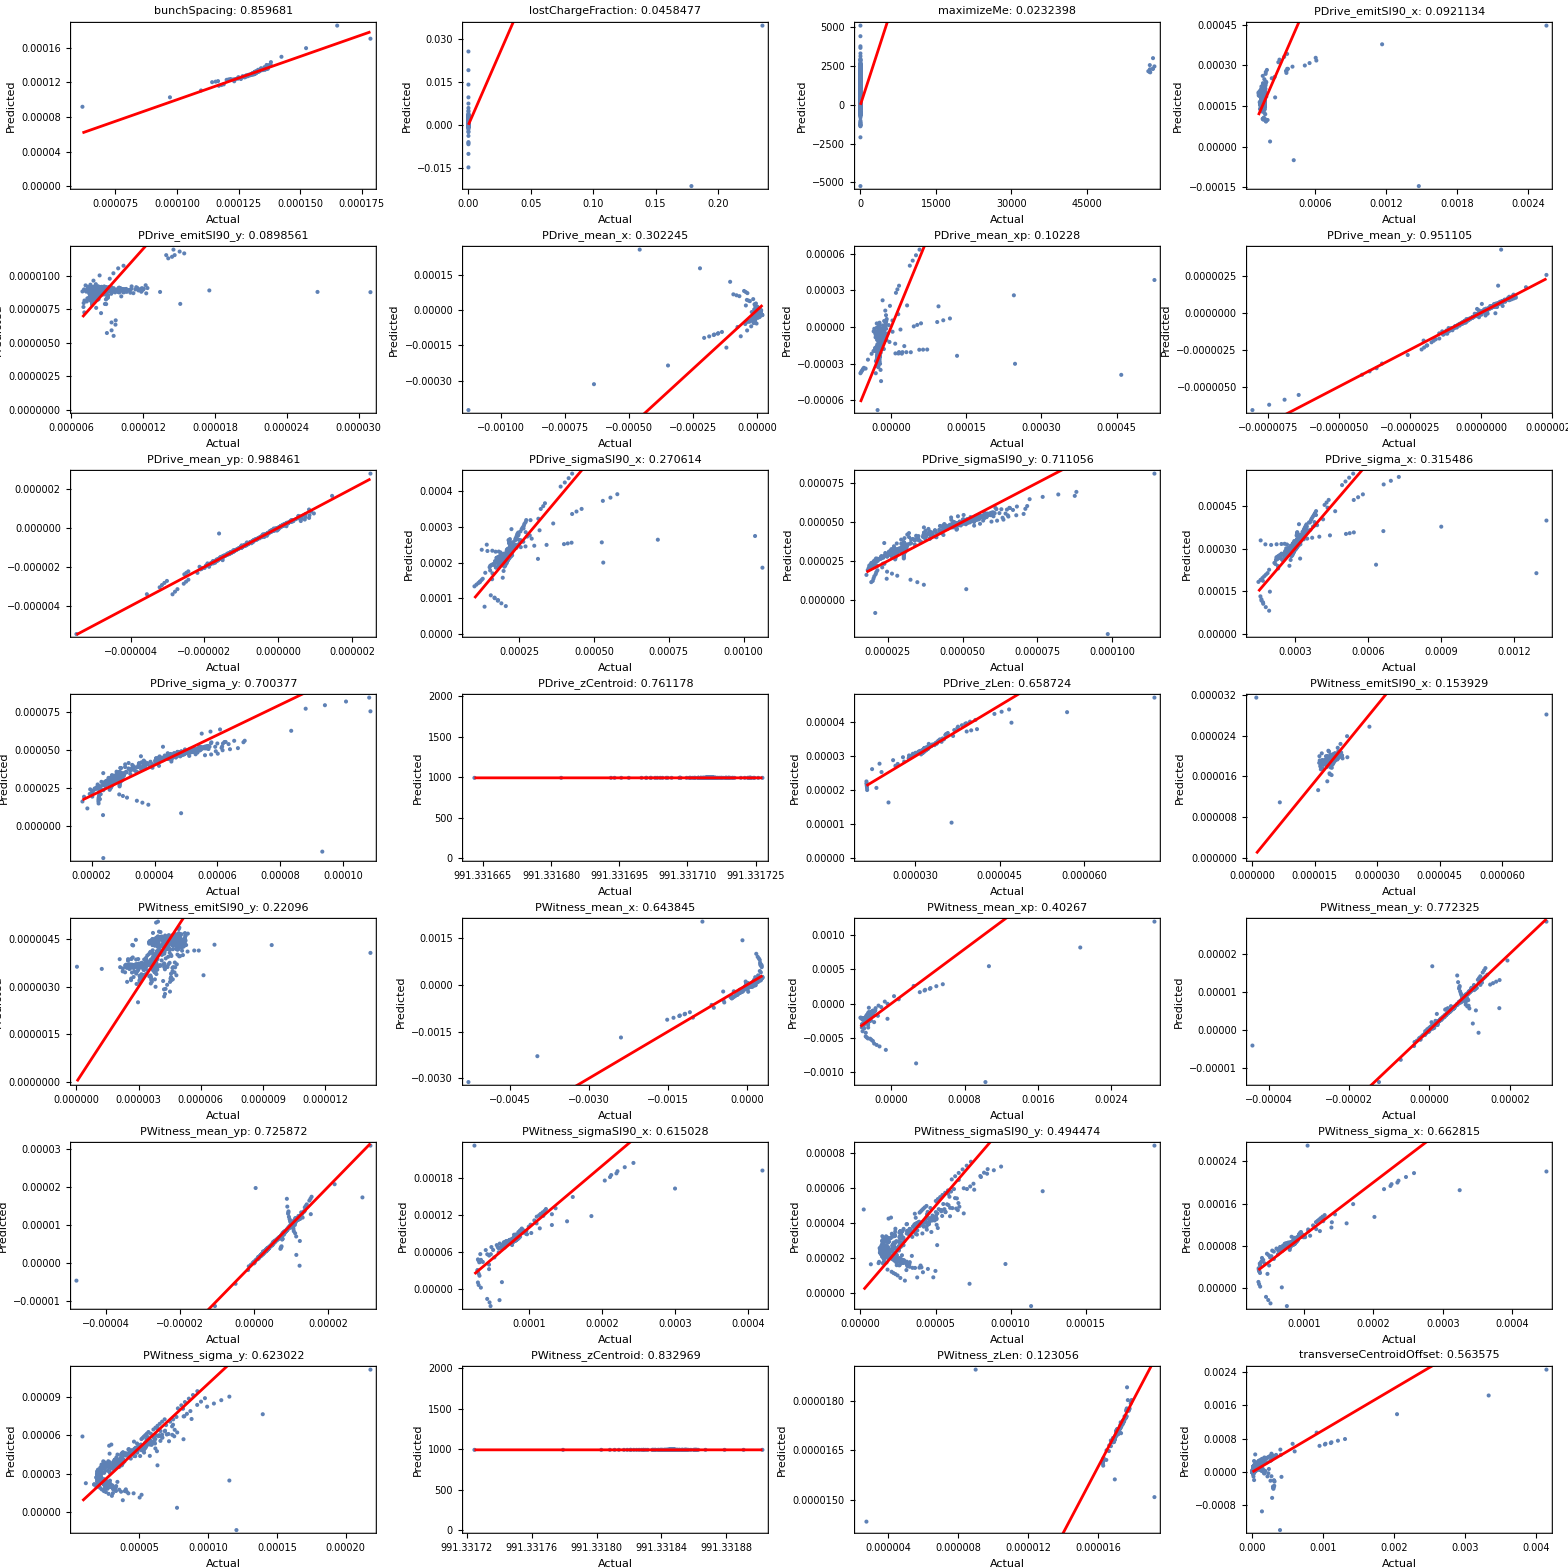

```mathematica
displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```